```mathematica
SetDirectory[NotebookDirectory[]]
```

E:\Documents\Homework\2014-Fall\AdvancedEmbeddedSystems\Project\teamRocket\testing\quadcopter-test\simulated-takeoff-20m-2014-11-09

```mathematica
data = Import["IMU4.TAB", "TSV"][[2;;]];
```

```mathematica
databar = Import["BARO4.TAB", "TSV"][[2;;]];
```

```mathematica
(##[[3]]&)/@({##[[2]]&/@data, ##[[3]]&/@data, ##[[4]]&/@data})
```

{0.00061,-0.005493,0.162964}

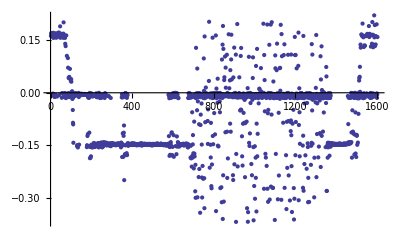

```mathematica
ListPlot[##[[4]]&/@data]
```

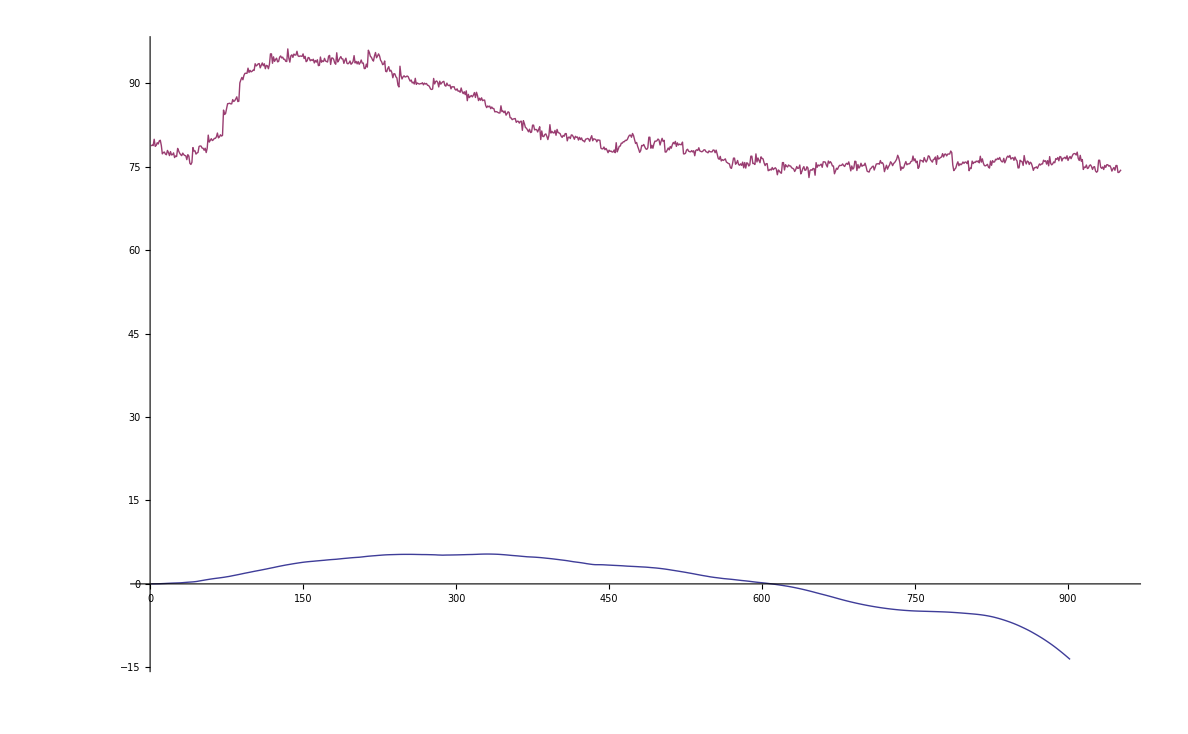

```mathematica
ListLinePlot[{-0.01* Accumulate[##[[4]]+0.09&/@data[[700;;]]]//Accumulate, ##[[3]]-200&/@databar[[700;;]]}]
```

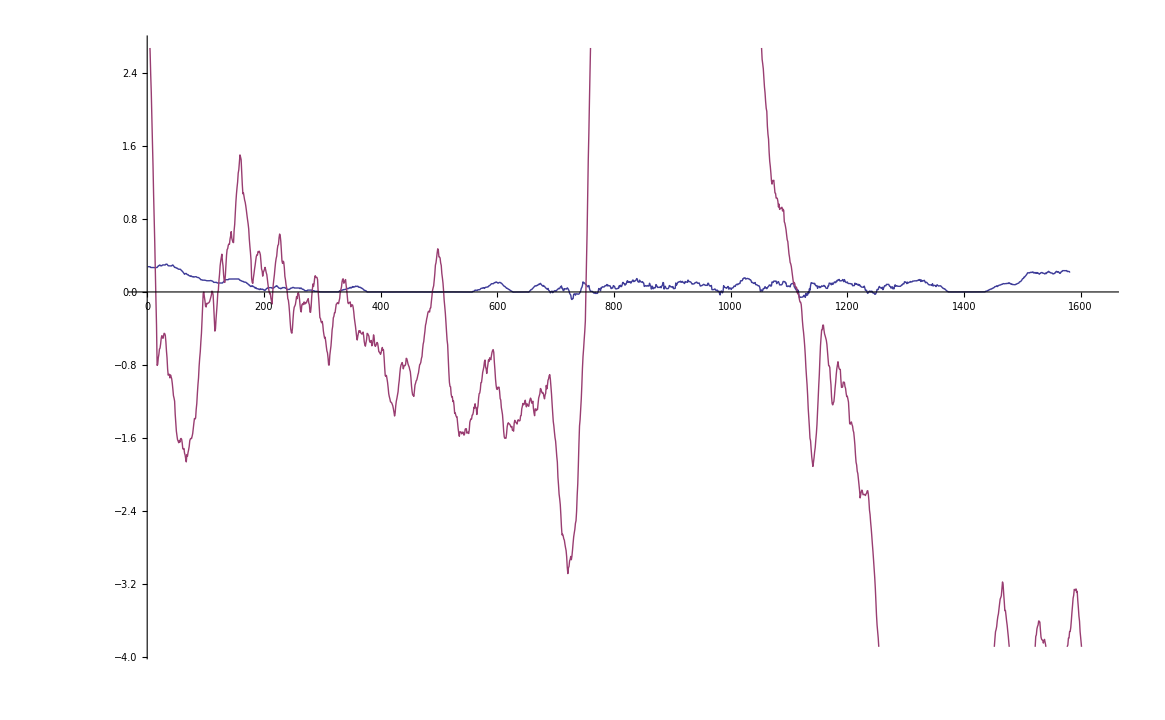

```mathematica
ListLinePlot[MovingAverage[##,20]&/@{##[[4]]+0.147&/@data,##[[3]]-280&/@databar}]
```

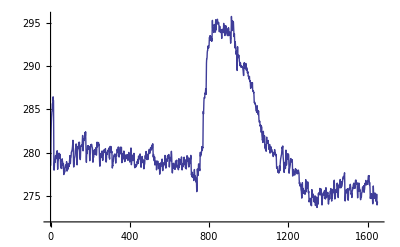

```mathematica
ListLinePlot[MovingAverage[##[[3]]&/@databar,2]]
```